```mathematica
Remove["Global`*"]
```

Generate a set of values that follow a Gaussian probability distribution then fit a binning of the data.

Choose values for mean u and standard deviation std. Generate n random numbers between -1 and +1.

```mathematica
u =10
std = 1
```

10

1

```mathematica
SeedRandom[10]
```

RandomGeneratorState[…]

```mathematica
n=RandomReal[{-1,1},10000]
```

{0.335833,0.667747,-0.0773686,-0.033475,0.904067,9990,-0.766481,-0.979913,0.0712523,-0.527152,-0.00248799}
 |  |  |  |

Turn the list into a list that is distributed according to the gaussian e^-t^2

```mathematica
ni = InverseErf[n]
```

{0.307003,0.685601,-0.0686739,-0.0296751,1.17726,9990,-0.842407,-1.64383,0.0632299,-0.507599,-0.00220493}
 |  |  |  |

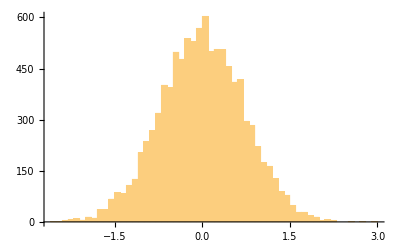

```mathematica
Histogram[ni,50]
```

Turn n list into a list containing select u and std values

```mathematica
l=ni*std+m;
```

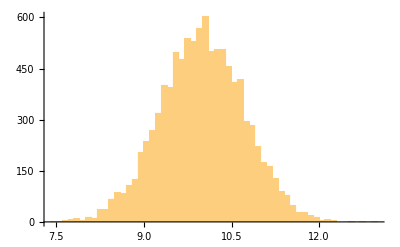

```mathematica
Histogram[l, 50]
```

Extract histogram frequencies and centers of the bins

```mathematica
xlo=Min[l]
xhi=Max[l]
dx=(xhi-xlo)/50
```

7.48287

12.9811

0.109966

```mathematica
r=Range[xlo,xhi,dx];
rr=r+.5*dx;
```

```mathematica
bc =BinCounts[l,{rr}];
cn = Delete[rr,51];
```

Plot of frequencies vs bin center

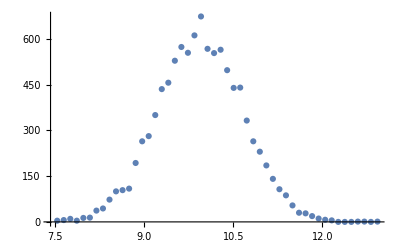

```mathematica
d = Transpose@{cn,bc};
ListPlot[d]
```

Integrating the Gaussian probability distribution P

```mathematica
P=1/(std*Sqrt[2 Pi])*E^(-((x-m)^2)/(2(std^2)))
```

(ⅇ^(-1/2 (-10+x)^2))/(√(2 π))

```mathematica
NIntegrate[P,{x,-100,100}]
```

1.

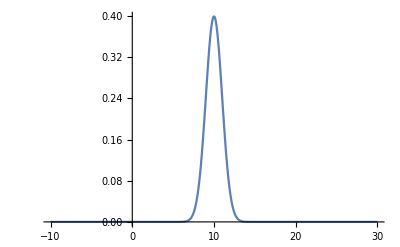

```mathematica
Plot[P,{x,-10,30}, PlotRange->Full]
```

```mathematica
px = FindFit[d,p*P,p,x]
```

{p→1266.63}

```mathematica
pfit = p/.px[[1]]
```

1266.63

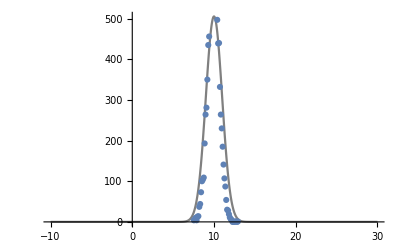

```mathematica
Show[Plot[pfit*P,{x,-10,30},PlotRange->Full,PlotStyle->Gray],ListPlot[d,PlotRange->Full,PlotStyle->Dashed]]
```